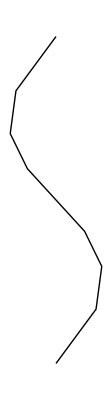
```mathematica
Module[{snip},
snip[pos_]:=
Arrowheads[
{{Automatic,
pos,
Graphics[
{BezierCurve[{{0,-(1/2)},{1/2,0},{-(1/2),0},{0,1/2}}]}
]
}}
];
Row[
{
Framed[
Column[{
Plot[
x^2/75^2*23,
{x,-75,75},
PlotRange->{{-75,75},{-30,40}},
Axes->{False,True},
AxesStyle->{None,snip[0.01]},
PlotStyle->Directive[PointSize[Large], RGBColor[0.35,0.6,0.95]],
ImageSize->350,
LabelStyle->{Black,Thick,16},
AxesLabel->{None,"E meV"}
],
Plot[-600,{x,-1,1},
Axes->{False,True},
AxesStyle->{None,Arrowheads[{{Automatic,0.01,-Graphics-},{Automatic,0.99,-Graphics-}}]},
PlotStyle->Directive[PointSize[Large], RGBColor[0.35,0.6,0.95],Dashed],
ImageSize->350,
LabelStyle->{Black,Thick,16},
PlotRange->{Automatic,{-650,-550}},
ImageSize->350
],
Plot[x^2/75^2*23-1420,
{x,-75,75},
PlotRange->{{-75,75},{-1420-10,60-1420}},
AxesStyle->{None,snip[0.99]},
AxesOrigin->{0,0},
PlotStyle->Directive[PointSize[Large], RGBColor[0.35,0.6,0.95]],
ImageSize->350,
LabelStyle->{Black,Thick,16},
Frame->{{False,False},{True,False}},
FrameLabel->"r nm"
]},
Alignment->Left,Spacings->0],
FrameStyle->{Black,Dashed}
],
Legended[
Framed[
Column[{
Plot[
x^2/75^2*40,
{x,-75,75},
PlotRange->{{-75,75},{-30,40}},
Axes->{False,True},
AxesStyle->{None,snip[0.01]},
PlotStyle->Directive[PointSize[Large], RGBColor[0.35,0.6,0.95]],
ImageSize->350,
LabelStyle->{Black,Thick,16},
AxesLabel->{None,"E meV"}
],
Plot[-600,{x,-1,1},
Axes->{False,True},
AxesStyle->{None,Arrowheads[{{Automatic,0.01,-Graphics-},{Automatic,0.99,-Graphics-}}]},
PlotStyle->Directive[PointSize[Large], RGBColor[0.35,0.6,0.95],Dashed],
ImageSize->350,
LabelStyle->{Black,Thick,16},
PlotRange->{Automatic,{-650,-550}},
ImageSize->350
],
Plot[x^2/75^2*40-1420,
{x,-75,75},
PlotRange->{{-75,75},{-1420-10,60-1420}},
AxesStyle->{None,snip[0.99]},
AxesOrigin->{0,0},
PlotStyle->Directive[PointSize[Large], RGBColor[0.35,0.6,0.95]],
ImageSize->350,
LabelStyle->{Black,Thick,16},
Frame->{{False,False},{True,False}},
FrameLabel->"r nm"
]},
Alignment->Left,Spacings->0],
FrameStyle->{Black,Dashed}
],
Style["E_F",Black,22]]
},
"     "
]
]
```

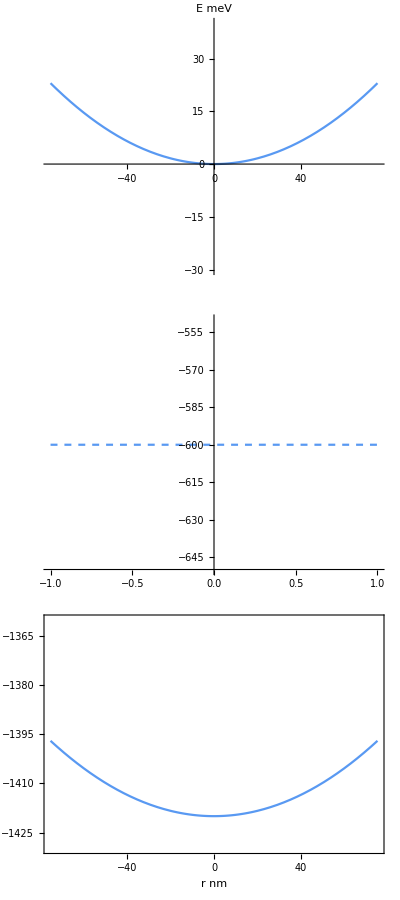
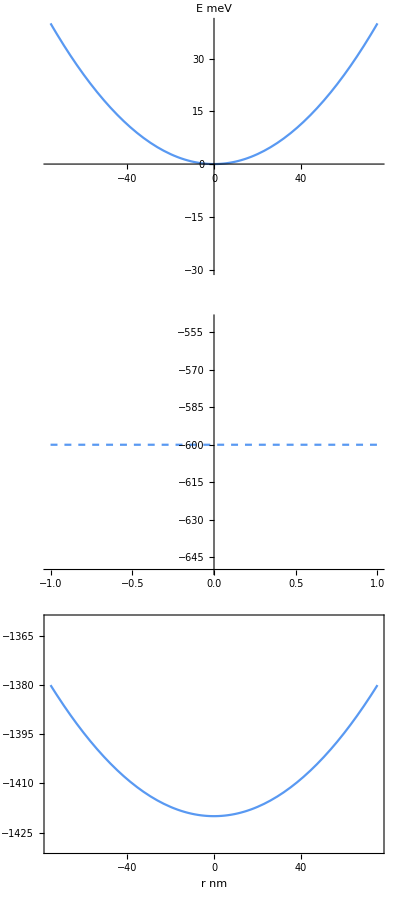

```mathematica
Legended
```